```mathematica
NS[]
```

```mathematica
matrix[n_]:=Block[{ff=Table[ToExpression["F"<>ToString[i]],{i,0,n}]},
f1=ff[[2;;]];
Prepend[
T@Prepend[
DiagonalMatrix[f1]-T[{f1}].{f1},
-f1*ff[[1]]],
Table[1,n+1]]]
```

```mathematica
matrix[3]//MF
```

(1 | 1 | 1 | 1
-F0 F1 | F1-F1^2 | -F1 F2 | -F1 F3
-F0 F2 | -F1 F2 | F2-F2^2 | -F2 F3
-F0 F3 | -F1 F3 | -F2 F3 | F3-F3^2)

```mathematica
ff=Table[ToExpression["F"<>ToString[i]],{i,0,n}],
f1=ff[[2;;]];
```

```mathematica
FS@Table[Det[matrix[i]],{i,2,6}]//MF
```

(-F1 F2 (-1-2 F0+F1+F2)
-F1 F2 F3 (-1-3 F0+F1+F2+F3)
-F1 F2 F3 F4 (-1-4 F0+F1+F2+F3+F4)
-F1 F2 F3 F4 F5 (-1-5 F0+F1+F2+F3+F4+F5)
-F1 F2 F3 F4 F5 F6 (-1-6 F0+F1+F2+F3+F4+F5+F6))

```mathematica
det[n_]:=Block[{ff=Table[ToExpression["F"<>ToString[i]],{i,0,n}]},
f1=ff[[2;;]];
Times@@ff*(n+1)]
```

```mathematica
FS@Table[det[i],{i,2,6}]//MF
```

(3 F0 F1 F2
4 F0 F1 F2 F3
5 F0 F1 F2 F3 F4
6 F0 F1 F2 F3 F4 F5
7 F0 F1 F2 F3 F4 F5 F6)

```mathematica
Table[
ff=Table[ToExpression["F"<>ToString[i]],{i,0,n}];
f1=ff[[2;;]];
Assuming[F0==1-Total@f1,
FS[Det[matrix[n]]==det[n]]],{n,2,5}]
```

{True,True,True,True}

```mathematica
matrixs[n_]:=Block[{ff=Table[ToExpression["F"<>ToString[i]],{i,0,n}]},
f1=ff[[2;;]];f0=ff[[1]];
DiagonalMatrix[f1]-T[{f1}].{f1-f0}]
```

```mathematica
matrixs[3]//MF
```

(F1-F1 (-F0+F1) | -F1 (-F0+F2) | -F1 (-F0+F3)
-(-F0+F1) F2 | F2-F2 (-F0+F2) | -F2 (-F0+F3)
-(-F0+F1) F3 | -(-F0+F2) F3 | F3-F3 (-F0+F3))

```mathematica
FS@Table[Det[matrixs[i]],{i,2,6}]//MF
```

(-F1 F2 (-1-2 F0+F1+F2)
-F1 F2 F3 (-1-3 F0+F1+F2+F3)
-F1 F2 F3 F4 (-1-4 F0+F1+F2+F3+F4)
-F1 F2 F3 F4 F5 (-1-5 F0+F1+F2+F3+F4+F5)
-F1 F2 F3 F4 F5 F6 (-1-6 F0+F1+F2+F3+F4+F5+F6))

```mathematica
dets[n_]:=Block[{ff=Table[ToExpression["F"<>ToString[i]],{i,0,n}]},
f1=ff[[2;;]];
Times@@ff*(n+1)]
```

```mathematica
FS@Table[dets[i],{i,2,6}]//MF
```

(3 F0 F1 F2
4 F0 F1 F2 F3
5 F0 F1 F2 F3 F4
6 F0 F1 F2 F3 F4 F5
7 F0 F1 F2 F3 F4 F5 F6)

```mathematica
Table[
ff=Table[ToExpression["F"<>ToString[i]],{i,0,n}];
f1=ff[[2;;]];
Assuming[F0==1-Total@f1,
FS[Det[matrixs[n]]==dets[n]]],{n,2,5}]
```

{True,True,True,True}

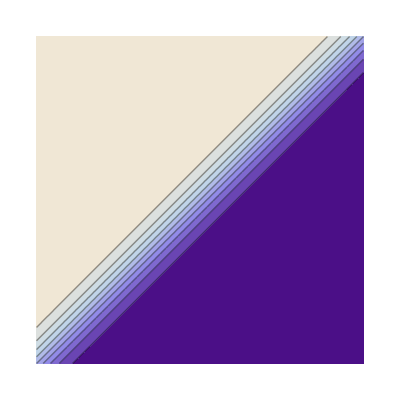

```mathematica
ContourPlot[Exp[t2]/(Exp[t1]+Exp[t2]),
{t1,-10,10},{t2,-10,10}]
```

```mathematica
rg1=-5;rg2=5;
p1=ContourPlot3D[Exp[t1]/(Exp[t1]+Exp[t2]+Exp[t3]),
{t1,rg1,rg2},{t2,rg1,rg2},{t3,rg1,rg2},Axes->True,Contours->Range[1,9,2]/10,Mesh->None,ContourStyle->Directive[Opacity[0.5]],AxesLabel->Auto,RegionFunction->Function[{x,y,z},-1/2<x+y+z<1/2]];p2=ContourPlot3D[Exp[t2]/(Exp[t1]+Exp[t2]+Exp[t3]),
{t1,rg1,rg2},{t2,rg1,rg2},{t3,rg1,rg2},Axes->True,Contours->Range[1,9,2]/10,Mesh->None,ContourStyle->Directive[Opacity[0.5]],AxesLabel->Auto,RegionFunction->Function[{x,y,z},-1/2<x+y+z<1/2]];p3=ContourPlot3D[Exp[t3]/(Exp[t1]+Exp[t2]+Exp[t3]),
{t1,rg1,rg2},{t2,rg1,rg2},{t3,rg1,rg2},Axes->True,Contours->Range[1,9,2]/10,Mesh->None,ContourStyle->Directive[Opacity[0.5]],AxesLabel->Auto,RegionFunction->Function[{x,y,z},-1/2<x+y+z<1/2]];
zs=ContourPlot3D[t1+t2+t3,
{t1,rg1,rg2},{t2,rg1,rg2},{t3,rg1,rg2},Axes->True,Contours->{0},Mesh->None,ContourStyle->Directive[Opacity[0.5]],AxesLabel->Auto];
```

```mathematica
Show[{p1,p2,p3,zs},ViewPoint->Dynamic[viewpoint]]
```

-Graphics3D-

```mathematica
expdf["exp_simplex",%]
```

exp_simplex.pdf

```mathematica
ContourPlot[Evaluate[{Exp[t1],Exp[t2]}/(Exp[t1]+Exp[t2])],
{t1,-10,10},{t2,-10,10}]
```

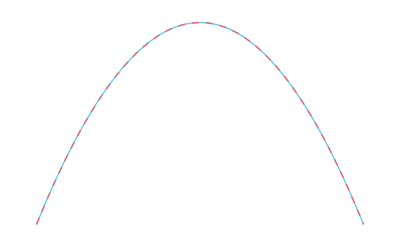

```mathematica
Plot[Evaluate[-5*10^5*r^2+{0,r}],{r,-0.01,0.01},PlotRange->All]
```

```mathematica
FindMaximum[-5*10^5*r^2+r,{r,0}]
```

{5.×10^-7,{r→9.999×10^-7}}

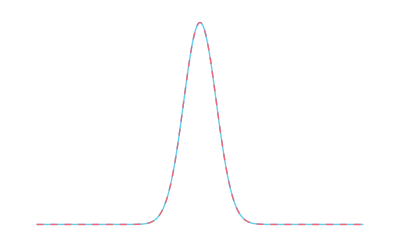

```mathematica
Plot[Evaluate@Exp[-5*10^5*r^2+{0,r}],{r,-0.01,0.01},PlotRange->All]
```